#### Background

This file computes and simplifies a cascaded phase sensor’s unitary matrix and converts it into a python-readable expressio.
It is a version of Juan José García Ripoll’s (Spanish Research Council (CSIC)) conversion script, modified to work with matrices. See: https://juanjose.garciaripoll.com/blog/converting-mathematica-to-python/index.html

#### Matrix-Building Methods

```mathematica
Clear["Global`*"]
(* Squeezing matrix of strength r, angle θ, in mode n, in a basis with m modes *)
Squeeze[r_, θ_, n_, M_] := Module[{mat, sqMat},
mat = IdentityMatrix[2M];
sqMat = {{Cosh[r]+Cos[θ]Sinh[r], Sin[θ]Sinh[r]},{Sin[θ]Sinh[r], Cosh[r]-Cos[θ]Sinh[r]}};
mat[[2n-1;;2n, 2n-1;;2n]] = sqMat;
mat
]

(* single-mode phase shift operator, with value ϕ on mode n in a basis with m modes *)
PS[ϕ_, n_, M_] := Module[{mat, PSMat},
mat = IdentityMatrix[2M];
PSMat = {{Cos[ϕ], -Sin[ϕ]},{Sin[ϕ], Cos[ϕ]}};
mat[[2n-1;;2n, 2n-1;;2n]] = PSMat;
mat
]

(* reflector (beamsplitter) matrix of strength T, acting between modes n1 and n2, in a basis with M modes *)
Refl[T_, n1_, n2_,M_] := Module[{mat},
mat = IdentityMatrix[2M];
mat[[2n1-1, 2n1-1]] = √T;
mat[[2n1, 2n1]] = √T;
mat[[2n2, 2n1]] = -√(1-T);
mat[[2n2-1, 2n1-1]] = -√(1-T);
mat[[2n1, 2n2]] = √(1-T);
mat[[2n1-1, 2n2-1]] = √(1-T);
mat[[2n2-1, 2n2-1]] = √T;
mat[[2n2, 2n2]] = √T;
mat
]

(* functions for loss in mode n of m 
use: d -> Loss1.d, σ-> Loss1.σ.Transpose[Loss1] + Loss2*)
Loss1[T_,n_, m_] := Table[If[i == j,If[(i == 2n || i == 2n-1),√(1-T),1],0],{i,1,2m},{j,1,2m}]
Loss2[T_, n_,m_] := Table[If[i == j && (i == 2n || i == 2n-1),1-T,0],{i,1,2m},{j,1,2m}]

(* function for plotting the Wigner function of the state, assuming α ~ 10 *)
W[x_,y_,d_, σ_] := 1/(√(π^2 Det[σ]))Exp[-(Transpose[{{x},{y}}-d].Inverse[σ].({{x},{y}}-d))[[1,1]]]+0.0001
PlotWigner[d_, σ_,textbool_,text_:""] :=Row[Table[DensityPlot[W[x,y,d[[2i-1;;2i]],σ[[2i-1;;2i,2i-1;;2i]]],{x,-15,+15},{y,-15,15},ColorFunction->"SunsetColors",PlotPoints->100,Axes->True,PlotRange->{Full, Full, {0,0.2}},FrameLabel->{{"Y",""},{"X",ToString[i]}},FrameStyle->Directive[Black, 16],ImageSize->300,PlotLegends->If[i == Length[d]/2, Automatic, None],AxesStyle->Directive[White],Epilog->If[(i == 1 && textbool),Inset[Framed[Style[text,16],Background->White],{0,13.2},{0,0}],Point[{14.8,14.8}]]],{i,1,Length[d]/2}]]
```

#### Python Conversion

```mathematica
(* primary methods provided by Juan José García Ripoll *)
ToPython[expression_,extravars_:{},outputvar_:"output",indent_:""]:=
Block[{
(* Python code that precedes our expression.
 Includes auxiliary vars and functions *)
PythonBuffer="",
(* Last number of defined variable *)
PythonVar=0,
(* Spaces to indent each line of Python code *)
PythonIndent=indent,
(* Was Sqrt[] used? Then we have to define it *)
PythonSqrt=False,
(* Was Pi used? We define π variable in Python *)
PythonPi=False},
(* We begin by parsing 'extravars' which is a list
{{var1, exp1},{var2,exp2},...}
of variables that are used in our formula. This is used for
simplifying expressions, as shown later on. *)
Do[
Module[{var=def[[1]],value=def[[2]]},
PythonBuffer=PythonBuffer<>PythonIndent<>ToString[var]<>"="<>ToPython2[value]<>";\n"],
{def,extravars}];
(*
  The actual conversion takes place here, recursively
 calling the function ToPython2, which does the work.
 *)
Module[{aux=ToPython2[expression]},
(* If Sqrt[] was used, we introduce a function that works with
  complex numbers, since np.sqrt does not *)
If[PythonSqrt,
PythonBuffer=PythonIndent<>"def mysqrt(x): return np.sqrt((1.+0j)*x)\n\n"<>PythonBuffer];
(* Define π as a Python variable *)
If[PythonPi,
PythonBuffer=PythonIndent<>"π=math.pi;\n\n"<>PythonBuffer];
(* Output Python code preceded by all variable definitions. *)
PythonBuffer<>PythonIndent<>outputvar<>"="<>aux<>";\n"]];

Clear[ToPythonVar];
ToPythonVar[a_]:=
Module[{name="aux"<>ToString[PythonVar]},
PythonBuffer=PythonBuffer<>PythonIndent<>name<>"="<>a<>";\n";
PythonVar=PythonVar+1;
name];

Clear[AlreadyWrapped];
AlreadyWrapped[s_]:=(StringPosition[s,"("]=={{1,1}})&&(StringPosition[s,")"]=={{StringLength[s],StringLength[s]}});

Clear[PythonWrap];
PythonWrap[expa_,limit_:70]:=
Module[{a=ToPython2[expa]},
If[StringLength[a]>limit,
ToPythonVar[a],
If[Not[AtomQ[expa]]&&!AlreadyWrapped[a],
"("<>a<>")",
a]]];

Clear[ToPython2];
(*ToPython2[Sqrt[x_]]:=Module[{},
PythonSqrt=True;
"mysqrt("<>PythonWrap[x]<>")"];*)
ToPython2[Sqrt[x]] := "np.sqrt(x)"
ToPython2[Log[x_]]:="np.log("<>PythonWrap[x]<>")"
ToPython2[Exp[x_]]:="np.exp("<>PythonWrap[x]<>")"
ToPython2[Sin[x_]]:="np.sin("<>PythonWrap[x]<>")"
ToPython2[Cos[x_]]:="np.cos("<>PythonWrap[x]<>")"
ToPython2[Sinh[x_]]:="np.sinh("<>PythonWrap[x]<>")"
ToPython2[Cosh[x_]]:="np.cosh("<>PythonWrap[x]<>")"
ToPython2[ⅇ^x_]:="np.exp("<>PythonWrap[x]<>")"
ToPython2[E^x_]:="np.exp("<>PythonWrap[x]<>")"
ToPython2[a_+b_]:=ToPythonOp["+",a,b]
ToPython2[a_*b_]:=ToPythonOp["*",a,b]
ToPython2[a_-b_]:=ToPythonOp["-",a,b]
ToPython2[a_/b_]:=ToPythonOp["/",a,b]
ToPython2[a_^2]:="("<>PythonWrap[a]<>"**2)"
ToPython2[a_^b_]:=PythonWrap[ToPythonOp["**",a,b]]
ToPython2[x_?NumberQ]:=
If[Head[x]===Complex,
"("<>ToPython2[Re[x]]<>"+"<>ToPython2[Im[x]]<>"j)",
ToString[N[x]]];
ToPython2[-x_]:="(-"<>ToPython2[x]<>")"
ToPython2[π]:=Module[{},PythonPi=True;"π"]
ToPython2[γ]:="γ"
ToPython2[Ω]:="Ω"
ToPython2[Δ]:="Δ"
ToPython2[x_]:=ToString[x];

(* This is for converting inline operations *)
Clear[ToPythonOp];
ToPythonOp[op_,expa_,expb_]:=
PythonWrap[expa]<>op<>PythonWrap[expb];

(* added method for matrix support *)
ToPythonMat[M_] := Module[{i,j},
ans = Table["", Length[M], Length[M]];
For[i = 1, i <= Length[M], i++,
For[j = 1, j <= Length[M[[1]]], j++,
ans[[i,j]] =StringReplace[ToPython[M[[i,j]]], {"output="-> "", ";"-> "","ϕ1"-> "p1", "ϕ2"-> "p2","ϕ3"-> "p3"}]
]];
ans = ToString[ans];
ans = StringReplace[ans, {"{"-> "[", "}"-> "]"}]
]
```

#### Use Case

```mathematica
(* matrix representing a three-phase interferometer with 10 modes *)
mat=PS[ϕ1,10,10].PS[ϕ2+ϕ3,1,10].Refl[1-T,1,10,10].PS[ϕ1,10,10].PS[ϕ3,9,10].PS[ϕ2,1,10].Refl[1-T,1,9,10].PS[ϕ3,9,10].PS[ϕ1,8,10].PS[ϕ2,1,10].Refl[1-T, 1,8,10].PS[ϕ1,8,10].PS[ϕ2,1,10].PS[ϕ3,7,10].Refl[1-T, 1,7,10].PS[ϕ3,7,10].PS[ϕ2,1,10].PS[ϕ1,6,10].Refl[1-T,1,6,10].PS[ϕ1,6,10].PS[ϕ2,1,10].PS[ϕ3,5,10].Refl[1-T,1,5,10].PS[ϕ3,5,10].PS[ϕ2,1,10].PS[ϕ1,4,10].Refl[1-T,1,4,10].PS[ϕ1,4,10].PS[ϕ2,1,10].PS[ϕ3,3,10].Refl[1-T,1,3,10].PS[ϕ3,3,10].PS[ϕ2,1,10].PS[ϕ1,2,10].Refl[T,1,2,10].PS[ϕ1,1,10]//FullSimplify;
mat//MatrixForm
```

((-1+T)^4 √T Cos[ϕ1+9 ϕ2+ϕ3] | -(-1+T)^4 √T Sin[ϕ1+9 ϕ2+ϕ3] | (1-T)^(9/2) Cos[9 ϕ2+ϕ3] | -(1-T)^(9/2) Sin[9 ϕ2+ϕ3] | -(-1+T)^3 √(-((-1+T) T)) Cos[2 (4 ϕ2+ϕ3)] | (-1+T)^3 √(-((-1+T) T)) Sin[2 (4 ϕ2+ϕ3)] | -(-1+T)^3 √T Cos[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 √T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^2 √(-((-1+T) T)) Cos[2 (3 ϕ2+ϕ3)] | -(-1+T)^2 √(-((-1+T) T)) Sin[2 (3 ϕ2+ϕ3)] | (-1+T)^2 √T Cos[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 √T Sin[ϕ1+5 ϕ2+ϕ3] | (1-T)^(3/2) √T Cos[2 (2 ϕ2+ϕ3)] | (-1+T) √(-((-1+T) T)) Sin[2 (2 ϕ2+ϕ3)] | -((-1+T) √T Cos[ϕ1+3 ϕ2+ϕ3]) | (-1+T) √T Sin[ϕ1+3 ϕ2+ϕ3] | √(-((-1+T) T)) Cos[2 (ϕ2+ϕ3)] | -√(-((-1+T) T)) Sin[2 (ϕ2+ϕ3)] | √T Cos[ϕ1+ϕ2+ϕ3] | -√T Sin[ϕ1+ϕ2+ϕ3]
(-1+T)^4 √T Sin[ϕ1+9 ϕ2+ϕ3] | (-1+T)^4 √T Cos[ϕ1+9 ϕ2+ϕ3] | (1-T)^(9/2) Sin[9 ϕ2+ϕ3] | (1-T)^(9/2) Cos[9 ϕ2+ϕ3] | -(-1+T)^3 √(-((-1+T) T)) Sin[2 (4 ϕ2+ϕ3)] | -(-1+T)^3 √(-((-1+T) T)) Cos[2 (4 ϕ2+ϕ3)] | -(-1+T)^3 √T Sin[ϕ1+7 ϕ2+ϕ3] | -(-1+T)^3 √T Cos[ϕ1+7 ϕ2+ϕ3] | (-1+T)^2 √(-((-1+T) T)) Sin[2 (3 ϕ2+ϕ3)] | (-1+T)^2 √(-((-1+T) T)) Cos[2 (3 ϕ2+ϕ3)] | (-1+T)^2 √T Sin[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 √T Cos[ϕ1+5 ϕ2+ϕ3] | (1-T)^(3/2) √T Sin[2 (2 ϕ2+ϕ3)] | (1-T)^(3/2) √T Cos[2 (2 ϕ2+ϕ3)] | -((-1+T) √T Sin[ϕ1+3 ϕ2+ϕ3]) | -((-1+T) √T Cos[ϕ1+3 ϕ2+ϕ3]) | √(-((-1+T) T)) Sin[2 (ϕ2+ϕ3)] | √(-((-1+T) T)) Cos[2 (ϕ2+ϕ3)] | √T Sin[ϕ1+ϕ2+ϕ3] | √T Cos[ϕ1+ϕ2+ϕ3]
-√(1-T) Cos[2 ϕ1] | √(1-T) Sin[2 ϕ1] | √T Cos[ϕ1] | -√T Sin[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 √(1-T) Cos[ϕ1] Sin[ϕ1] | -√(1-T) Cos[2 ϕ1] | √T Sin[ϕ1] | √T Cos[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | -√(-((-1+T) T)) Cos[ϕ2+ϕ3] | √(-((-1+T) T)) Sin[ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | -√(-((-1+T) T)) Sin[ϕ2+ϕ3] | -√(-((-1+T) T)) Cos[ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | (-1+T) √T Cos[ϕ1+2 ϕ2] | -((-1+T) √T Sin[ϕ1+2 ϕ2]) | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | (-1+T) √T Sin[ϕ1+2 ϕ2] | (-1+T) √T Cos[ϕ1+2 ϕ2] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | (-1+T) √(-((-1+T) T)) Cos[3 ϕ2+ϕ3] | (1-T)^(3/2) √T Sin[3 ϕ2+ϕ3] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | √(1-T) T Sin[2 (ϕ2+ϕ3)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | (-1+T) √(-((-1+T) T)) Sin[3 ϕ2+ϕ3] | (-1+T) √(-((-1+T) T)) Cos[3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ2+ϕ3)] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(-1+T)^2 √T Cos[ϕ1+4 ϕ2] | (-1+T)^2 √T Sin[ϕ1+4 ϕ2] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | -(-1+T)^2 √T Sin[ϕ1+4 ϕ2] | -(-1+T)^2 √T Cos[ϕ1+4 ϕ2] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 √(-((-1+T) T)) Cos[5 ϕ2+ϕ3] | (-1+T)^2 √(-((-1+T) T)) Sin[5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | √(1-T) T Sin[2 (ϕ2+ϕ3)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0 | 0 | 0 | 0 | 0
-(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 √(-((-1+T) T)) Sin[5 ϕ2+ϕ3] | -(-1+T)^2 √(-((-1+T) T)) Cos[5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ2+ϕ3)] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0 | 0 | 0 | 0 | 0
-(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | (1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | (-1+T)^3 √T Cos[ϕ1+6 ϕ2] | -(-1+T)^3 √T Sin[ϕ1+6 ϕ2] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1] | 0 | 0 | 0 | 0
-(1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | -(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | (-1+T)^3 √T Sin[ϕ1+6 ϕ2] | (-1+T)^3 √T Cos[ϕ1+6 ϕ2] | -(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1] | 0 | 0 | 0 | 0
(-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 √(-((-1+T) T)) Cos[7 ϕ2+ϕ3] | -(-1+T)^3 √(-((-1+T) T)) Sin[7 ϕ2+ϕ3] | -(1-T)^(5/2) T Cos[2 (3 ϕ2+ϕ3)] | (1-T)^(5/2) T Sin[2 (3 ϕ2+ϕ3)] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | √(1-T) T Sin[2 (ϕ2+ϕ3)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0
(-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 √(-((-1+T) T)) Sin[7 ϕ2+ϕ3] | (-1+T)^3 √(-((-1+T) T)) Cos[7 ϕ2+ϕ3] | -(1-T)^(5/2) T Sin[2 (3 ϕ2+ϕ3)] | -(1-T)^(5/2) T Cos[2 (3 ϕ2+ϕ3)] | -(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ2+ϕ3)] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0
-(1-T)^(7/2) T Cos[2 (ϕ1+4 ϕ2)] | (1-T)^(7/2) T Sin[2 (ϕ1+4 ϕ2)] | -(-1+T)^4 √T Cos[ϕ1+8 ϕ2] | (-1+T)^4 √T Sin[ϕ1+8 ϕ2] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | -(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | (1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1]
-(1-T)^(7/2) T Sin[2 (ϕ1+4 ϕ2)] | -(1-T)^(7/2) T Cos[2 (ϕ1+4 ϕ2)] | -(-1+T)^4 √T Sin[ϕ1+8 ϕ2] | -(-1+T)^4 √T Cos[ϕ1+8 ϕ2] | (-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | -(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | -(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1])

```mathematica
(* similar matrix with 12 modes *)
mat2=PS[ϕ1,12,12].PS[ϕ2+ϕ3,1,12].Refl[1-T,1,12,12].PS[ϕ1,12,12].PS[ϕ3,11,12].PS[ϕ2,1,12].Refl[1-T,1,11,12].PS[ϕ3, 11, 12].PS[ϕ1,10,12].PS[ϕ2,1,12].Refl[1-T,1,10,12].PS[ϕ1,10,12].PS[ϕ3,9,12].PS[ϕ2,1,12].Refl[1-T,1,9,12].PS[ϕ3,9,12].PS[ϕ1,8,12].PS[ϕ2,1,12].Refl[1-T, 1,8,12].PS[ϕ1,8,12].PS[ϕ2,1,12].PS[ϕ3,7,12].Refl[1-T, 1,7,12].PS[ϕ3,7,12].PS[ϕ2,1,12].PS[ϕ1,6,12].Refl[1-T,1,6,12].PS[ϕ1,6,12].PS[ϕ2,1,12].PS[ϕ3,5,12].Refl[1-T,1,5,12].PS[ϕ3,5,12].PS[ϕ2,1,12].PS[ϕ1,4,12].Refl[1-T,1,4,12].PS[ϕ1,4,12].PS[ϕ2,1,12].PS[ϕ3,3,12].Refl[1-T,1,3,12].PS[ϕ3,3,12].PS[ϕ2,1,12].PS[ϕ1,2,12].Refl[T,1,2,12].PS[ϕ1,1,12]//FullSimplify;
```

```mathematica
mat2//MatrixForm
```

(-(-1+T)^5 √T Cos[ϕ1+11 ϕ2+ϕ3] | (-1+T)^5 √T Sin[ϕ1+11 ϕ2+ϕ3] | (1-T)^(11/2) Cos[11 ϕ2+ϕ3] | -(1-T)^(11/2) Sin[11 ϕ2+ϕ3] | (-1+T)^4 √(-((-1+T) T)) Cos[2 (5 ϕ2+ϕ3)] | -(-1+T)^4 √(-((-1+T) T)) Sin[2 (5 ϕ2+ϕ3)] | (-1+T)^4 √T Cos[ϕ1+9 ϕ2+ϕ3] | -(-1+T)^4 √T Sin[ϕ1+9 ϕ2+ϕ3] | -(-1+T)^3 √(-((-1+T) T)) Cos[2 (4 ϕ2+ϕ3)] | (-1+T)^3 √(-((-1+T) T)) Sin[2 (4 ϕ2+ϕ3)] | -(-1+T)^3 √T Cos[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 √T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^2 √(-((-1+T) T)) Cos[2 (3 ϕ2+ϕ3)] | -(-1+T)^2 √(-((-1+T) T)) Sin[2 (3 ϕ2+ϕ3)] | (-1+T)^2 √T Cos[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 √T Sin[ϕ1+5 ϕ2+ϕ3] | (1-T)^(3/2) √T Cos[2 (2 ϕ2+ϕ3)] | (-1+T) √(-((-1+T) T)) Sin[2 (2 ϕ2+ϕ3)] | -((-1+T) √T Cos[ϕ1+3 ϕ2+ϕ3]) | (-1+T) √T Sin[ϕ1+3 ϕ2+ϕ3] | √(-((-1+T) T)) Cos[2 (ϕ2+ϕ3)] | -√(-((-1+T) T)) Sin[2 (ϕ2+ϕ3)] | √T Cos[ϕ1+ϕ2+ϕ3] | -√T Sin[ϕ1+ϕ2+ϕ3]
-(-1+T)^5 √T Sin[ϕ1+11 ϕ2+ϕ3] | -(-1+T)^5 √T Cos[ϕ1+11 ϕ2+ϕ3] | (1-T)^(11/2) Sin[11 ϕ2+ϕ3] | (1-T)^(11/2) Cos[11 ϕ2+ϕ3] | (-1+T)^4 √(-((-1+T) T)) Sin[2 (5 ϕ2+ϕ3)] | (-1+T)^4 √(-((-1+T) T)) Cos[2 (5 ϕ2+ϕ3)] | (-1+T)^4 √T Sin[ϕ1+9 ϕ2+ϕ3] | (-1+T)^4 √T Cos[ϕ1+9 ϕ2+ϕ3] | -(-1+T)^3 √(-((-1+T) T)) Sin[2 (4 ϕ2+ϕ3)] | -(-1+T)^3 √(-((-1+T) T)) Cos[2 (4 ϕ2+ϕ3)] | -(-1+T)^3 √T Sin[ϕ1+7 ϕ2+ϕ3] | -(-1+T)^3 √T Cos[ϕ1+7 ϕ2+ϕ3] | (-1+T)^2 √(-((-1+T) T)) Sin[2 (3 ϕ2+ϕ3)] | (-1+T)^2 √(-((-1+T) T)) Cos[2 (3 ϕ2+ϕ3)] | (-1+T)^2 √T Sin[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 √T Cos[ϕ1+5 ϕ2+ϕ3] | (1-T)^(3/2) √T Sin[2 (2 ϕ2+ϕ3)] | (1-T)^(3/2) √T Cos[2 (2 ϕ2+ϕ3)] | -((-1+T) √T Sin[ϕ1+3 ϕ2+ϕ3]) | -((-1+T) √T Cos[ϕ1+3 ϕ2+ϕ3]) | √(-((-1+T) T)) Sin[2 (ϕ2+ϕ3)] | √(-((-1+T) T)) Cos[2 (ϕ2+ϕ3)] | √T Sin[ϕ1+ϕ2+ϕ3] | √T Cos[ϕ1+ϕ2+ϕ3]
-√(1-T) Cos[2 ϕ1] | √(1-T) Sin[2 ϕ1] | √T Cos[ϕ1] | -√T Sin[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 √(1-T) Cos[ϕ1] Sin[ϕ1] | -√(1-T) Cos[2 ϕ1] | √T Sin[ϕ1] | √T Cos[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | -√(-((-1+T) T)) Cos[ϕ2+ϕ3] | √(-((-1+T) T)) Sin[ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | -√(-((-1+T) T)) Sin[ϕ2+ϕ3] | -√(-((-1+T) T)) Cos[ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | (-1+T) √T Cos[ϕ1+2 ϕ2] | -((-1+T) √T Sin[ϕ1+2 ϕ2]) | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | (-1+T) √T Sin[ϕ1+2 ϕ2] | (-1+T) √T Cos[ϕ1+2 ϕ2] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | (-1+T) √(-((-1+T) T)) Cos[3 ϕ2+ϕ3] | (1-T)^(3/2) √T Sin[3 ϕ2+ϕ3] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | √(1-T) T Sin[2 (ϕ2+ϕ3)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | (-1+T) √(-((-1+T) T)) Sin[3 ϕ2+ϕ3] | (-1+T) √(-((-1+T) T)) Cos[3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ2+ϕ3)] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(-1+T)^2 √T Cos[ϕ1+4 ϕ2] | (-1+T)^2 √T Sin[ϕ1+4 ϕ2] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | -(-1+T)^2 √T Sin[ϕ1+4 ϕ2] | -(-1+T)^2 √T Cos[ϕ1+4 ϕ2] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 √(-((-1+T) T)) Cos[5 ϕ2+ϕ3] | (-1+T)^2 √(-((-1+T) T)) Sin[5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | √(1-T) T Sin[2 (ϕ2+ϕ3)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 √(-((-1+T) T)) Sin[5 ϕ2+ϕ3] | -(-1+T)^2 √(-((-1+T) T)) Cos[5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ2+ϕ3)] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | (1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | (-1+T)^3 √T Cos[ϕ1+6 ϕ2] | -(-1+T)^3 √T Sin[ϕ1+6 ϕ2] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | -(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | (-1+T)^3 √T Sin[ϕ1+6 ϕ2] | (-1+T)^3 √T Cos[ϕ1+6 ϕ2] | -(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 √(-((-1+T) T)) Cos[7 ϕ2+ϕ3] | -(-1+T)^3 √(-((-1+T) T)) Sin[7 ϕ2+ϕ3] | -(1-T)^(5/2) T Cos[2 (3 ϕ2+ϕ3)] | (1-T)^(5/2) T Sin[2 (3 ϕ2+ϕ3)] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | √(1-T) T Sin[2 (ϕ2+ϕ3)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0 | 0 | 0 | 0 | 0
(-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 √(-((-1+T) T)) Sin[7 ϕ2+ϕ3] | (-1+T)^3 √(-((-1+T) T)) Cos[7 ϕ2+ϕ3] | -(1-T)^(5/2) T Sin[2 (3 ϕ2+ϕ3)] | -(1-T)^(5/2) T Cos[2 (3 ϕ2+ϕ3)] | -(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ2+ϕ3)] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0 | 0 | 0 | 0 | 0
-(1-T)^(7/2) T Cos[2 (ϕ1+4 ϕ2)] | (1-T)^(7/2) T Sin[2 (ϕ1+4 ϕ2)] | -(-1+T)^4 √T Cos[ϕ1+8 ϕ2] | (-1+T)^4 √T Sin[ϕ1+8 ϕ2] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | -(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | (1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1] | 0 | 0 | 0 | 0
-(1-T)^(7/2) T Sin[2 (ϕ1+4 ϕ2)] | -(1-T)^(7/2) T Cos[2 (ϕ1+4 ϕ2)] | -(-1+T)^4 √T Sin[ϕ1+8 ϕ2] | -(-1+T)^4 √T Cos[ϕ1+8 ϕ2] | (-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | -(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | -(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1] | 0 | 0 | 0 | 0
-(-1+T)^4 T Cos[ϕ1+9 ϕ2+ϕ3] | (-1+T)^4 T Sin[ϕ1+9 ϕ2+ϕ3] | -(-1+T)^4 √(-((-1+T) T)) Cos[9 ϕ2+ϕ3] | (-1+T)^4 √(-((-1+T) T)) Sin[9 ϕ2+ϕ3] | -(1-T)^(7/2) T Cos[2 (4 ϕ2+ϕ3)] | (1-T)^(7/2) T Sin[2 (4 ϕ2+ϕ3)] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | -(1-T)^(5/2) T Cos[2 (3 ϕ2+ϕ3)] | (1-T)^(5/2) T Sin[2 (3 ϕ2+ϕ3)] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | √(1-T) T Sin[2 (ϕ2+ϕ3)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ3] | -2 √(1-T) Cos[ϕ3] Sin[ϕ3] | 0 | 0
-(-1+T)^4 T Sin[ϕ1+9 ϕ2+ϕ3] | -(-1+T)^4 T Cos[ϕ1+9 ϕ2+ϕ3] | -(-1+T)^4 √(-((-1+T) T)) Sin[9 ϕ2+ϕ3] | -(-1+T)^4 √(-((-1+T) T)) Cos[9 ϕ2+ϕ3] | -(1-T)^(7/2) T Sin[2 (4 ϕ2+ϕ3)] | -(1-T)^(7/2) T Cos[2 (4 ϕ2+ϕ3)] | (-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(1-T)^(5/2) T Sin[2 (3 ϕ2+ϕ3)] | -(1-T)^(5/2) T Cos[2 (3 ϕ2+ϕ3)] | -(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (2 ϕ2+ϕ3)] | -(1-T)^(3/2) T Cos[2 (2 ϕ2+ϕ3)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ2+ϕ3)] | -√(1-T) T Cos[2 (ϕ2+ϕ3)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ3] | √(1-T) Cos[2 ϕ3] | 0 | 0
-(1-T)^(9/2) T Cos[2 (ϕ1+5 ϕ2)] | (1-T)^(9/2) T Sin[2 (ϕ1+5 ϕ2)] | (-1+T)^5 √T Cos[ϕ1+10 ϕ2] | -(-1+T)^5 √T Sin[ϕ1+10 ϕ2] | -(-1+T)^4 T Cos[ϕ1+9 ϕ2+ϕ3] | (-1+T)^4 T Sin[ϕ1+9 ϕ2+ϕ3] | -(1-T)^(7/2) T Cos[2 (ϕ1+4 ϕ2)] | (1-T)^(7/2) T Sin[2 (ϕ1+4 ϕ2)] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | -(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | (1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | (-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -((-1+T) T Sin[ϕ1+3 ϕ2+ϕ3]) | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | √(1-T) T Sin[2 (ϕ1+ϕ2)] | -T Cos[ϕ1+ϕ2+ϕ3] | T Sin[ϕ1+ϕ2+ϕ3] | √(1-T) Cos[2 ϕ1] | -2 √(1-T) Cos[ϕ1] Sin[ϕ1]
-(1-T)^(9/2) T Sin[2 (ϕ1+5 ϕ2)] | -(1-T)^(9/2) T Cos[2 (ϕ1+5 ϕ2)] | (-1+T)^5 √T Sin[ϕ1+10 ϕ2] | (-1+T)^5 √T Cos[ϕ1+10 ϕ2] | -(-1+T)^4 T Sin[ϕ1+9 ϕ2+ϕ3] | -(-1+T)^4 T Cos[ϕ1+9 ϕ2+ϕ3] | -(1-T)^(7/2) T Sin[2 (ϕ1+4 ϕ2)] | -(1-T)^(7/2) T Cos[2 (ϕ1+4 ϕ2)] | (-1+T)^3 T Sin[ϕ1+7 ϕ2+ϕ3] | (-1+T)^3 T Cos[ϕ1+7 ϕ2+ϕ3] | -(1-T)^(5/2) T Sin[2 (ϕ1+3 ϕ2)] | -(1-T)^(5/2) T Cos[2 (ϕ1+3 ϕ2)] | -(-1+T)^2 T Sin[ϕ1+5 ϕ2+ϕ3] | -(-1+T)^2 T Cos[ϕ1+5 ϕ2+ϕ3] | -(1-T)^(3/2) T Sin[2 (ϕ1+2 ϕ2)] | -(1-T)^(3/2) T Cos[2 (ϕ1+2 ϕ2)] | (-1+T) T Sin[ϕ1+3 ϕ2+ϕ3] | (-1+T) T Cos[ϕ1+3 ϕ2+ϕ3] | -√(1-T) T Sin[2 (ϕ1+ϕ2)] | -√(1-T) T Cos[2 (ϕ1+ϕ2)] | -T Sin[ϕ1+ϕ2+ϕ3] | -T Cos[ϕ1+ϕ2+ϕ3] | √(1-T) Sin[2 ϕ1] | √(1-T) Cos[2 ϕ1])

```mathematica
ToPythonMat[mat2] (* copy / paste into python script *)
```

[[(-((-1.+T)**5.)*((T**0.5)*(np.cos((p1+((11.*p2)+p3)))))), ((-1.+T)**5.)*((T**0.5)*(np.sin((p1+((11.*p2)+p3))))), ((1.-T)**5.5)*(np.cos(((11.*p2)+p3))), (-((1.-T)**5.5)*(np.sin(((11.*p2)+p3)))), ((-1.+T)**4.)*((((-(-1.+T)*T))**0.5)*(np.cos((2.*((5.*p2)+p3))))), (-((-1.+T)**4.)*((((-(-1.+T)*T))**0.5)*(np.sin((2.*((5.*p2)+p3)))))), ((-1.+T)**4.)*((T**0.5)*(np.cos((p1+((9.*p2)+p3))))), (-((-1.+T)**4.)*((T**0.5)*(np.sin((p1+((9.*p2)+p3)))))), (-((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.cos((2.*((4.*p2)+p3)))))), ((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.sin((2.*((4.*p2)+p3))))), (-((-1.+T)**3.)*((T**0.5)*(np.cos((p1+((7.*p2)+p3)))))), ((-1.+T)**3.)*((T**0.5)*(np.sin((p1+((7.*p2)+p3))))), (((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.cos((2.*((3.*p2)+p3))))), (-(((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.sin((2.*((3.*p2)+p3)))))), (((-1.+T)**2))*((T**0.5)*(np.cos((p1+((5.*p2)+p3))))), (-(((-1.+T)**2))*((T**0.5)*(np.sin((p1+((5.*p2)+p3)))))), ((1.-T)**1.5)*((T**0.5)*(np.cos((2.*((2.*p2)+p3))))), (-1.+T)*((((-(-1.+T)*T))**0.5)*(np.sin((2.*((2.*p2)+p3))))), (-(-1.+T)*((T**0.5)*(np.cos((p1+((3.*p2)+p3)))))), (-1.+T)*((T**0.5)*(np.sin((p1+((3.*p2)+p3))))), (((-(-1.+T)*T))**0.5)*(np.cos((2.*(p2+p3)))), (-(((-(-1.+T)*T))**0.5)*(np.sin((2.*(p2+p3))))), (T**0.5)*(np.cos((p1+(p2+p3)))), (-(T**0.5)*(np.sin((p1+(p2+p3)))))], [(-((-1.+T)**5.)*((T**0.5)*(np.sin((p1+((11.*p2)+p3)))))), (-((-1.+T)**5.)*((T**0.5)*(np.cos((p1+((11.*p2)+p3)))))), ((1.-T)**5.5)*(np.sin(((11.*p2)+p3))), ((1.-T)**5.5)*(np.cos(((11.*p2)+p3))), ((-1.+T)**4.)*((((-(-1.+T)*T))**0.5)*(np.sin((2.*((5.*p2)+p3))))), ((-1.+T)**4.)*((((-(-1.+T)*T))**0.5)*(np.cos((2.*((5.*p2)+p3))))), ((-1.+T)**4.)*((T**0.5)*(np.sin((p1+((9.*p2)+p3))))), ((-1.+T)**4.)*((T**0.5)*(np.cos((p1+((9.*p2)+p3))))), (-((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.sin((2.*((4.*p2)+p3)))))), (-((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.cos((2.*((4.*p2)+p3)))))), (-((-1.+T)**3.)*((T**0.5)*(np.sin((p1+((7.*p2)+p3)))))), (-((-1.+T)**3.)*((T**0.5)*(np.cos((p1+((7.*p2)+p3)))))), (((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.sin((2.*((3.*p2)+p3))))), (((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.cos((2.*((3.*p2)+p3))))), (((-1.+T)**2))*((T**0.5)*(np.sin((p1+((5.*p2)+p3))))), (((-1.+T)**2))*((T**0.5)*(np.cos((p1+((5.*p2)+p3))))), ((1.-T)**1.5)*((T**0.5)*(np.sin((2.*((2.*p2)+p3))))), ((1.-T)**1.5)*((T**0.5)*(np.cos((2.*((2.*p2)+p3))))), (-(-1.+T)*((T**0.5)*(np.sin((p1+((3.*p2)+p3)))))), (-(-1.+T)*((T**0.5)*(np.cos((p1+((3.*p2)+p3)))))), (((-(-1.+T)*T))**0.5)*(np.sin((2.*(p2+p3)))), (((-(-1.+T)*T))**0.5)*(np.cos((2.*(p2+p3)))), (T**0.5)*(np.sin((p1+(p2+p3)))), (T**0.5)*(np.cos((p1+(p2+p3))))], [(-((1.-T)**0.5)*(np.cos((2.*p1)))), ((1.-T)**0.5)*(np.sin((2.*p1))), (T**0.5)*(np.cos(p1)), (-(T**0.5)*(np.sin(p1))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [-2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), (-((1.-T)**0.5)*(np.cos((2.*p1)))), (T**0.5)*(np.sin(p1)), (T**0.5)*(np.cos(p1)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), (-(((-(-1.+T)*T))**0.5)*(np.cos((p2+p3)))), (((-(-1.+T)*T))**0.5)*(np.sin((p2+p3))), ((1.-T)**0.5)*(np.cos((2.*p3))), -2.*(((1.-T)**0.5)*((np.cos(p3))*(np.sin(p3)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), (-(((-(-1.+T)*T))**0.5)*(np.sin((p2+p3)))), (-(((-(-1.+T)*T))**0.5)*(np.cos((p2+p3)))), ((1.-T)**0.5)*(np.sin((2.*p3))), ((1.-T)**0.5)*(np.cos((2.*p3))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2))))), (-1.+T)*((T**0.5)*(np.cos((p1+(2.*p2))))), (-(-1.+T)*((T**0.5)*(np.sin((p1+(2.*p2)))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), (-1.+T)*((T**0.5)*(np.sin((p1+(2.*p2))))), (-1.+T)*((T**0.5)*(np.cos((p1+(2.*p2))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3)))))), (-1.+T)*((((-(-1.+T)*T))**0.5)*(np.cos(((3.*p2)+p3)))), ((1.-T)**1.5)*((T**0.5)*(np.sin(((3.*p2)+p3)))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p2+p3)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p3))), -2.*(((1.-T)**0.5)*((np.cos(p3))*(np.sin(p3)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-1.+T)*((((-(-1.+T)*T))**0.5)*(np.sin(((3.*p2)+p3)))), (-1.+T)*((((-(-1.+T)*T))**0.5)*(np.cos(((3.*p2)+p3)))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p2+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p2+p3)))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p3))), ((1.-T)**0.5)*(np.cos((2.*p3))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-(((-1.+T)**2))*((T**0.5)*(np.cos((p1+(4.*p2)))))), (((-1.+T)**2))*((T**0.5)*(np.sin((p1+(4.*p2))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-(((-1.+T)**2))*((T**0.5)*(np.sin((p1+(4.*p2)))))), (-(((-1.+T)**2))*((T**0.5)*(np.cos((p1+(4.*p2)))))), (-1.+T)*(T*(np.sin((p1+((3.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3))))), (-(((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.cos(((5.*p2)+p3))))), (((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.sin(((5.*p2)+p3)))), (-((1.-T)**1.5)*(T*(np.cos((2.*((2.*p2)+p3)))))), ((1.-T)**1.5)*(T*(np.sin((2.*((2.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p2+p3)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p3))), -2.*(((1.-T)**0.5)*((np.cos(p3))*(np.sin(p3)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-(((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (-(((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.sin(((5.*p2)+p3))))), (-(((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.cos(((5.*p2)+p3))))), (-((1.-T)**1.5)*(T*(np.sin((2.*((2.*p2)+p3)))))), (-((1.-T)**1.5)*(T*(np.cos((2.*((2.*p2)+p3)))))), (-1.+T)*(T*(np.sin((p1+((3.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p2+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p2+p3)))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p3))), ((1.-T)**0.5)*(np.cos((2.*p3))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(3.*p2))))))), ((1.-T)**2.5)*(T*(np.sin((2.*(p1+(3.*p2)))))), ((-1.+T)**3.)*((T**0.5)*(np.cos((p1+(6.*p2))))), (-((-1.+T)**3.)*((T**0.5)*(np.sin((p1+(6.*p2)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**2.5)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(3.*p2))))))), ((-1.+T)**3.)*((T**0.5)*(np.sin((p1+(6.*p2))))), ((-1.+T)**3.)*((T**0.5)*(np.cos((p1+(6.*p2))))), (-(((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-1.+T)*(T*(np.sin((p1+((3.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0., 0., 0., 0., 0.], [((-1.+T)**3.)*(T*(np.cos((p1+((7.*p2)+p3))))), (-((-1.+T)**3.)*(T*(np.sin((p1+((7.*p2)+p3)))))), ((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.cos(((7.*p2)+p3)))), (-((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.sin(((7.*p2)+p3))))), (-((1.-T)**2.5)*(T*(np.cos((2.*((3.*p2)+p3)))))), ((1.-T)**2.5)*(T*(np.sin((2.*((3.*p2)+p3))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3))))), (-((1.-T)**1.5)*(T*(np.cos((2.*((2.*p2)+p3)))))), ((1.-T)**1.5)*(T*(np.sin((2.*((2.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p2+p3)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p3))), -2.*(((1.-T)**0.5)*((np.cos(p3))*(np.sin(p3)))), 0., 0., 0., 0., 0., 0.], [((-1.+T)**3.)*(T*(np.sin((p1+((7.*p2)+p3))))), ((-1.+T)**3.)*(T*(np.cos((p1+((7.*p2)+p3))))), ((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.sin(((7.*p2)+p3)))), ((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.cos(((7.*p2)+p3)))), (-((1.-T)**2.5)*(T*(np.sin((2.*((3.*p2)+p3)))))), (-((1.-T)**2.5)*(T*(np.cos((2.*((3.*p2)+p3)))))), (-(((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (-((1.-T)**1.5)*(T*(np.sin((2.*((2.*p2)+p3)))))), (-((1.-T)**1.5)*(T*(np.cos((2.*((2.*p2)+p3)))))), (-1.+T)*(T*(np.sin((p1+((3.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p2+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p2+p3)))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p3))), ((1.-T)**0.5)*(np.cos((2.*p3))), 0., 0., 0., 0., 0., 0.], [(-((1.-T)**3.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), ((1.-T)**3.5)*(T*(np.sin((2.*(p1+(4.*p2)))))), (-((-1.+T)**4.)*((T**0.5)*(np.cos((p1+(8.*p2)))))), ((-1.+T)**4.)*((T**0.5)*(np.sin((p1+(8.*p2))))), ((-1.+T)**3.)*(T*(np.cos((p1+((7.*p2)+p3))))), (-((-1.+T)**3.)*(T*(np.sin((p1+((7.*p2)+p3)))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(3.*p2))))))), ((1.-T)**2.5)*(T*(np.sin((2.*(p1+(3.*p2)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0.], [(-((1.-T)**3.5)*(T*(np.sin((2.*(p1+(4.*p2))))))), (-((1.-T)**3.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), (-((-1.+T)**4.)*((T**0.5)*(np.sin((p1+(8.*p2)))))), (-((-1.+T)**4.)*((T**0.5)*(np.cos((p1+(8.*p2)))))), ((-1.+T)**3.)*(T*(np.sin((p1+((7.*p2)+p3))))), ((-1.+T)**3.)*(T*(np.cos((p1+((7.*p2)+p3))))), (-((1.-T)**2.5)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(3.*p2))))))), (-(((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-1.+T)*(T*(np.sin((p1+((3.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0.], [(-((-1.+T)**4.)*(T*(np.cos((p1+((9.*p2)+p3)))))), ((-1.+T)**4.)*(T*(np.sin((p1+((9.*p2)+p3))))), (-((-1.+T)**4.)*((((-(-1.+T)*T))**0.5)*(np.cos(((9.*p2)+p3))))), ((-1.+T)**4.)*((((-(-1.+T)*T))**0.5)*(np.sin(((9.*p2)+p3)))), (-((1.-T)**3.5)*(T*(np.cos((2.*((4.*p2)+p3)))))), ((1.-T)**3.5)*(T*(np.sin((2.*((4.*p2)+p3))))), ((-1.+T)**3.)*(T*(np.cos((p1+((7.*p2)+p3))))), (-((-1.+T)**3.)*(T*(np.sin((p1+((7.*p2)+p3)))))), (-((1.-T)**2.5)*(T*(np.cos((2.*((3.*p2)+p3)))))), ((1.-T)**2.5)*(T*(np.sin((2.*((3.*p2)+p3))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3))))), (-((1.-T)**1.5)*(T*(np.cos((2.*((2.*p2)+p3)))))), ((1.-T)**1.5)*(T*(np.sin((2.*((2.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p2+p3)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p3))), -2.*(((1.-T)**0.5)*((np.cos(p3))*(np.sin(p3)))), 0., 0.], [(-((-1.+T)**4.)*(T*(np.sin((p1+((9.*p2)+p3)))))), (-((-1.+T)**4.)*(T*(np.cos((p1+((9.*p2)+p3)))))), (-((-1.+T)**4.)*((((-(-1.+T)*T))**0.5)*(np.sin(((9.*p2)+p3))))), (-((-1.+T)**4.)*((((-(-1.+T)*T))**0.5)*(np.cos(((9.*p2)+p3))))), (-((1.-T)**3.5)*(T*(np.sin((2.*((4.*p2)+p3)))))), (-((1.-T)**3.5)*(T*(np.cos((2.*((4.*p2)+p3)))))), ((-1.+T)**3.)*(T*(np.sin((p1+((7.*p2)+p3))))), ((-1.+T)**3.)*(T*(np.cos((p1+((7.*p2)+p3))))), (-((1.-T)**2.5)*(T*(np.sin((2.*((3.*p2)+p3)))))), (-((1.-T)**2.5)*(T*(np.cos((2.*((3.*p2)+p3)))))), (-(((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (-((1.-T)**1.5)*(T*(np.sin((2.*((2.*p2)+p3)))))), (-((1.-T)**1.5)*(T*(np.cos((2.*((2.*p2)+p3)))))), (-1.+T)*(T*(np.sin((p1+((3.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p2+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p2+p3)))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p3))), ((1.-T)**0.5)*(np.cos((2.*p3))), 0., 0.], [(-((1.-T)**4.5)*(T*(np.cos((2.*(p1+(5.*p2))))))), ((1.-T)**4.5)*(T*(np.sin((2.*(p1+(5.*p2)))))), ((-1.+T)**5.)*((T**0.5)*(np.cos((p1+(10.*p2))))), (-((-1.+T)**5.)*((T**0.5)*(np.sin((p1+(10.*p2)))))), (-((-1.+T)**4.)*(T*(np.cos((p1+((9.*p2)+p3)))))), ((-1.+T)**4.)*(T*(np.sin((p1+((9.*p2)+p3))))), (-((1.-T)**3.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), ((1.-T)**3.5)*(T*(np.sin((2.*(p1+(4.*p2)))))), ((-1.+T)**3.)*(T*(np.cos((p1+((7.*p2)+p3))))), (-((-1.+T)**3.)*(T*(np.sin((p1+((7.*p2)+p3)))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(3.*p2))))))), ((1.-T)**2.5)*(T*(np.sin((2.*(p1+(3.*p2)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-(-1.+T)*(T*(np.sin((p1+((3.*p2)+p3)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((p1+(p2+p3))))), T*(np.sin((p1+(p2+p3)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1))))], [(-((1.-T)**4.5)*(T*(np.sin((2.*(p1+(5.*p2))))))), (-((1.-T)**4.5)*(T*(np.cos((2.*(p1+(5.*p2))))))), ((-1.+T)**5.)*((T**0.5)*(np.sin((p1+(10.*p2))))), ((-1.+T)**5.)*((T**0.5)*(np.cos((p1+(10.*p2))))), (-((-1.+T)**4.)*(T*(np.sin((p1+((9.*p2)+p3)))))), (-((-1.+T)**4.)*(T*(np.cos((p1+((9.*p2)+p3)))))), (-((1.-T)**3.5)*(T*(np.sin((2.*(p1+(4.*p2))))))), (-((1.-T)**3.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), ((-1.+T)**3.)*(T*(np.sin((p1+((7.*p2)+p3))))), ((-1.+T)**3.)*(T*(np.cos((p1+((7.*p2)+p3))))), (-((1.-T)**2.5)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(3.*p2))))))), (-(((-1.+T)**2))*(T*(np.sin((p1+((5.*p2)+p3)))))), (-(((-1.+T)**2))*(T*(np.cos((p1+((5.*p2)+p3)))))), (-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-1.+T)*(T*(np.sin((p1+((3.*p2)+p3))))), (-1.+T)*(T*(np.cos((p1+((3.*p2)+p3))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+p2)))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+p2)))))), (-T*(np.sin((p1+(p2+p3))))), (-T*(np.cos((p1+(p2+p3))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1)))]]

```mathematica
mat2/.{ϕ1->0, ϕ2-> 0, ϕ3->0, T-> 0.5} (* test case *)
```

{{0.015625,0.,0.015625,0.,0.0220971,0.,0.03125,0.,0.0441942,0.,0.0625,0.,0.0883883,0.,0.125,0.,0.176777,0.,0.25,0.,0.353553,0.,0.5,0.},{0.,0.015625,0.,0.015625,0.,0.0220971,0.,0.03125,0.,0.0441942,0.,0.0625,0.,0.0883883,0.,0.125,0.,0.176777,0.,0.25,0.,0.353553,0.,0.5},{-0.707107,0.,0.707107,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,-0.707107,0.,0.707107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.5,0.,-0.5,0.,0.707107,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,-0.5,0.,-0.5,0.,0.707107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.353553,0.,-0.353553,0.,-0.5,0.,0.707107,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,-0.353553,0.,-0.353553,0.,-0.5,0.,0.707107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.25,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,-0.25,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.176777,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0.,0,0,0,0,0,0,0,0,0,0,0,0},{0.,-0.176777,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0,0,0,0,0,0,0,0,0,0,0,0},{-0.125,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0.,0,0,0,0,0,0,0,0,0,0},{0.,-0.125,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0,0,0,0,0,0,0,0,0,0},{-0.0883883,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0.,0,0,0,0,0,0,0,0},{0.,-0.0883883,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0,0,0,0,0,0,0,0},{-0.0625,0.,-0.0625,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0.,0,0,0,0,0,0},{0.,-0.0625,0.,-0.0625,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0,0,0,0,0,0},{-0.0441942,0.,-0.0441942,0.,-0.0625,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0.,0,0,0,0},{0.,-0.0441942,0.,-0.0441942,0.,-0.0625,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0,0,0,0},{-0.03125,0.,-0.03125,0.,-0.0441942,0.,-0.0625,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0.,0,0},{0.,-0.03125,0.,-0.03125,0.,-0.0441942,0.,-0.0625,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0,0},{-0.0220971,0.,-0.0220971,0.,-0.03125,0.,-0.0441942,0.,-0.0625,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107,0.},{0.,-0.0220971,0.,-0.0220971,0.,-0.03125,0.,-0.0441942,0.,-0.0625,0.,-0.0883883,0.,-0.125,0.,-0.176777,0.,-0.25,0.,-0.353553,0.,-0.5,0.,0.707107}}

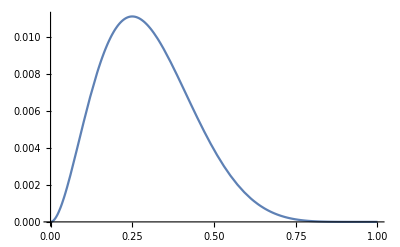

```mathematica
Plot[T^2(1-T)^6,{T,0,1}] (*7 modes is sufficient for 1% accuracy *)
```

```mathematica
m = 10; (* matrix for a 2-phase, one-sided sensor (mirror after ϕ2). *)
mat2b = PS[ϕ1,10,m].PS[2ϕ2+ϕ1,1,m].Refl[1-T, 1,10,m].PS[ϕ1,10,m].PS[ϕ1,9,m].PS[2ϕ2,1,m].Refl[1-T, 1,9,m].PS[ϕ1,9,m].PS[ϕ1,8,m].PS[2ϕ2,1,m].Refl[1-T, 1,8,m].PS[ϕ1,8,m].PS[ϕ1,7,m].PS[2ϕ2,1,m].Refl[1-T, 1,7,m].PS[ϕ1,7,m].PS[ϕ1,6,m].PS[2ϕ2,1,m].Refl[1-T, 1,6,m].PS[ϕ1,6,m].PS[ϕ1,5,m].PS[2ϕ2,1,m].Refl[1-T, 1,5,m].PS[ϕ1,5,m].PS[ϕ1,4,m].PS[2ϕ2,1,m].Refl[1-T, 1,4,m].PS[ϕ1,4,m].PS[ϕ1,3,m].PS[2ϕ2,1,m].Refl[1-T, 1,3,m].PS[ϕ1,2,m].PS[ϕ1,3,m].PS[2ϕ2, 1,m].Refl[T,1,2,m].PS[ϕ2,2,m].PS[ϕ1,1,m]//FullSimplify;
```

```mathematica
d = Table[{0},20]; (* test case *)
d[[1]] = {α};
mat2b.d//FullSimplify//MatrixForm
```

((-1+T)^4 √T α Cos[2 (ϕ1+9 ϕ2)]
(-1+T)^4 √T α Sin[2 (ϕ1+9 ϕ2)]
-√(1-T) α Cos[2 ϕ1]
-2 √(1-T) α Cos[ϕ1] Sin[ϕ1]
-T α Cos[2 (ϕ1+ϕ2)]
-T α Sin[2 (ϕ1+ϕ2)]
-√(1-T) T α Cos[2 (ϕ1+2 ϕ2)]
-√(1-T) T α Sin[2 (ϕ1+2 ϕ2)]
(-1+T) T α Cos[2 (ϕ1+3 ϕ2)]
(-1+T) T α Sin[2 (ϕ1+3 ϕ2)]
-(1-T)^(3/2) T α Cos[2 (ϕ1+4 ϕ2)]
-(1-T)^(3/2) T α Sin[2 (ϕ1+4 ϕ2)]
-(-1+T)^2 T α Cos[2 (ϕ1+5 ϕ2)]
-(-1+T)^2 T α Sin[2 (ϕ1+5 ϕ2)]
-(1-T)^(5/2) T α Cos[2 (ϕ1+6 ϕ2)]
-(1-T)^(5/2) T α Sin[2 (ϕ1+6 ϕ2)]
(-1+T)^3 T α Cos[2 (ϕ1+7 ϕ2)]
(-1+T)^3 T α Sin[2 (ϕ1+7 ϕ2)]
-(1-T)^(7/2) T α Cos[2 (ϕ1+8 ϕ2)]
-(1-T)^(7/2) T α Sin[2 (ϕ1+8 ϕ2)])

```mathematica
ToPythonMat[mat2b]
```

[[((-1.+T)**4.)*((T**0.5)*(np.cos((2.*(p1+(9.*p2)))))), (-((-1.+T)**4.)*((T**0.5)*(np.sin((2.*(p1+(9.*p2))))))), ((1.-T)**4.5)*(np.cos((p1+(19.*p2)))), (-((1.-T)**4.5)*(np.sin((p1+(19.*p2))))), (-((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.cos((2.*(p1+(8.*p2))))))), ((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.sin((2.*(p1+(8.*p2)))))), (-((-1.+T)**3.)*((T**0.5)*(np.cos((2.*(p1+(7.*p2))))))), ((-1.+T)**3.)*((T**0.5)*(np.sin((2.*(p1+(7.*p2)))))), (((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.cos((2.*(p1+(6.*p2)))))), (-(((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.sin((2.*(p1+(6.*p2))))))), (((-1.+T)**2))*((T**0.5)*(np.cos((2.*(p1+(5.*p2)))))), (-(((-1.+T)**2))*((T**0.5)*(np.sin((2.*(p1+(5.*p2))))))), ((1.-T)**1.5)*((T**0.5)*(np.cos((2.*(p1+(4.*p2)))))), (-1.+T)*((((-(-1.+T)*T))**0.5)*(np.sin((2.*(p1+(4.*p2)))))), (-(-1.+T)*((T**0.5)*(np.cos((2.*(p1+(3.*p2))))))), (-1.+T)*((T**0.5)*(np.sin((2.*(p1+(3.*p2)))))), (((-(-1.+T)*T))**0.5)*(np.cos((2.*(p1+(2.*p2))))), (-(((-(-1.+T)*T))**0.5)*(np.sin((2.*(p1+(2.*p2)))))), (T**0.5)*(np.cos((2.*(p1+p2)))), (-(T**0.5)*(np.sin((2.*(p1+p2)))))], [((-1.+T)**4.)*((T**0.5)*(np.sin((2.*(p1+(9.*p2)))))), ((-1.+T)**4.)*((T**0.5)*(np.cos((2.*(p1+(9.*p2)))))), ((1.-T)**4.5)*(np.sin((p1+(19.*p2)))), ((1.-T)**4.5)*(np.cos((p1+(19.*p2)))), (-((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.sin((2.*(p1+(8.*p2))))))), (-((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.cos((2.*(p1+(8.*p2))))))), (-((-1.+T)**3.)*((T**0.5)*(np.sin((2.*(p1+(7.*p2))))))), (-((-1.+T)**3.)*((T**0.5)*(np.cos((2.*(p1+(7.*p2))))))), (((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.sin((2.*(p1+(6.*p2)))))), (((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.cos((2.*(p1+(6.*p2)))))), (((-1.+T)**2))*((T**0.5)*(np.sin((2.*(p1+(5.*p2)))))), (((-1.+T)**2))*((T**0.5)*(np.cos((2.*(p1+(5.*p2)))))), ((1.-T)**1.5)*((T**0.5)*(np.sin((2.*(p1+(4.*p2)))))), ((1.-T)**1.5)*((T**0.5)*(np.cos((2.*(p1+(4.*p2)))))), (-(-1.+T)*((T**0.5)*(np.sin((2.*(p1+(3.*p2))))))), (-(-1.+T)*((T**0.5)*(np.cos((2.*(p1+(3.*p2))))))), (((-(-1.+T)*T))**0.5)*(np.sin((2.*(p1+(2.*p2))))), (((-(-1.+T)*T))**0.5)*(np.cos((2.*(p1+(2.*p2))))), (T**0.5)*(np.sin((2.*(p1+p2)))), (T**0.5)*(np.cos((2.*(p1+p2))))], [(-((1.-T)**0.5)*(np.cos((2.*p1)))), ((1.-T)**0.5)*(np.sin((2.*p1))), (T**0.5)*(np.cos((p1+p2))), (-(T**0.5)*(np.sin((p1+p2)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [-2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), (-((1.-T)**0.5)*(np.cos((2.*p1)))), (T**0.5)*(np.sin((p1+p2))), (T**0.5)*(np.cos((p1+p2))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-T*(np.cos((2.*(p1+p2))))), T*(np.sin((2.*(p1+p2)))), (-(((-(-1.+T)*T))**0.5)*(np.cos((p1+(3.*p2))))), (((-(-1.+T)*T))**0.5)*(np.sin((p1+(3.*p2)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((2.*(p1+p2))))), (-(((-(-1.+T)*T))**0.5)*(np.sin((p1+(3.*p2))))), (-(((-(-1.+T)*T))**0.5)*(np.cos((p1+(3.*p2))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-1.+T)*((T**0.5)*(np.cos((p1+(5.*p2))))), (-(-1.+T)*((T**0.5)*(np.sin((p1+(5.*p2)))))), (-T*(np.cos((2.*(p1+p2))))), T*(np.sin((2.*(p1+p2)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-1.+T)*((T**0.5)*(np.sin((p1+(5.*p2))))), (-1.+T)*((T**0.5)*(np.cos((p1+(5.*p2))))), (-T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((2.*(p1+p2))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-(-1.+T)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-1.+T)*((((-(-1.+T)*T))**0.5)*(np.cos((p1+(7.*p2))))), ((1.-T)**1.5)*((T**0.5)*(np.sin((p1+(7.*p2))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-T*(np.cos((2.*(p1+p2))))), T*(np.sin((2.*(p1+p2)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-1.+T)*(T*(np.sin((2.*(p1+(3.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-1.+T)*((((-(-1.+T)*T))**0.5)*(np.sin((p1+(7.*p2))))), (-1.+T)*((((-(-1.+T)*T))**0.5)*(np.cos((p1+(7.*p2))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((2.*(p1+p2))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2)))))), (-(((-1.+T)**2))*((T**0.5)*(np.cos((p1+(9.*p2)))))), (((-1.+T)**2))*((T**0.5)*(np.sin((p1+(9.*p2))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-(-1.+T)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-T*(np.cos((2.*(p1+p2))))), T*(np.sin((2.*(p1+p2)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0., 0., 0., 0., 0.], [(-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), (-(((-1.+T)**2))*((T**0.5)*(np.sin((p1+(9.*p2)))))), (-(((-1.+T)**2))*((T**0.5)*(np.cos((p1+(9.*p2)))))), (-1.+T)*(T*(np.sin((2.*(p1+(3.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((2.*(p1+p2))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0., 0., 0., 0., 0.], [(-(((-1.+T)**2))*(T*(np.cos((2.*(p1+(5.*p2))))))), (((-1.+T)**2))*(T*(np.sin((2.*(p1+(5.*p2)))))), (-(((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.cos((p1+(11.*p2)))))), (((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.sin((p1+(11.*p2))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-(-1.+T)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-T*(np.cos((2.*(p1+p2))))), T*(np.sin((2.*(p1+p2)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0., 0., 0.], [(-(((-1.+T)**2))*(T*(np.sin((2.*(p1+(5.*p2))))))), (-(((-1.+T)**2))*(T*(np.cos((2.*(p1+(5.*p2))))))), (-(((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.sin((p1+(11.*p2)))))), (-(((-1.+T)**2))*((((-(-1.+T)*T))**0.5)*(np.cos((p1+(11.*p2)))))), (-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), (-1.+T)*(T*(np.sin((2.*(p1+(3.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((2.*(p1+p2))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0., 0., 0.], [(-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(6.*p2))))))), ((1.-T)**2.5)*(T*(np.sin((2.*(p1+(6.*p2)))))), ((-1.+T)**3.)*((T**0.5)*(np.cos((p1+(13.*p2))))), (-((-1.+T)**3.)*((T**0.5)*(np.sin((p1+(13.*p2)))))), (-(((-1.+T)**2))*(T*(np.cos((2.*(p1+(5.*p2))))))), (((-1.+T)**2))*(T*(np.sin((2.*(p1+(5.*p2)))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-(-1.+T)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-T*(np.cos((2.*(p1+p2))))), T*(np.sin((2.*(p1+p2)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0., 0., 0.], [(-((1.-T)**2.5)*(T*(np.sin((2.*(p1+(6.*p2))))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(6.*p2))))))), ((-1.+T)**3.)*((T**0.5)*(np.sin((p1+(13.*p2))))), ((-1.+T)**3.)*((T**0.5)*(np.cos((p1+(13.*p2))))), (-(((-1.+T)**2))*(T*(np.sin((2.*(p1+(5.*p2))))))), (-(((-1.+T)**2))*(T*(np.cos((2.*(p1+(5.*p2))))))), (-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), (-1.+T)*(T*(np.sin((2.*(p1+(3.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((2.*(p1+p2))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0., 0., 0.], [((-1.+T)**3.)*(T*(np.cos((2.*(p1+(7.*p2)))))), (-((-1.+T)**3.)*(T*(np.sin((2.*(p1+(7.*p2))))))), ((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.cos((p1+(15.*p2))))), (-((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.sin((p1+(15.*p2)))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(6.*p2))))))), ((1.-T)**2.5)*(T*(np.sin((2.*(p1+(6.*p2)))))), (-(((-1.+T)**2))*(T*(np.cos((2.*(p1+(5.*p2))))))), (((-1.+T)**2))*(T*(np.sin((2.*(p1+(5.*p2)))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-(-1.+T)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-T*(np.cos((2.*(p1+p2))))), T*(np.sin((2.*(p1+p2)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1)))), 0., 0.], [((-1.+T)**3.)*(T*(np.sin((2.*(p1+(7.*p2)))))), ((-1.+T)**3.)*(T*(np.cos((2.*(p1+(7.*p2)))))), ((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.sin((p1+(15.*p2))))), ((-1.+T)**3.)*((((-(-1.+T)*T))**0.5)*(np.cos((p1+(15.*p2))))), (-((1.-T)**2.5)*(T*(np.sin((2.*(p1+(6.*p2))))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(6.*p2))))))), (-(((-1.+T)**2))*(T*(np.sin((2.*(p1+(5.*p2))))))), (-(((-1.+T)**2))*(T*(np.cos((2.*(p1+(5.*p2))))))), (-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), (-1.+T)*(T*(np.sin((2.*(p1+(3.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((2.*(p1+p2))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1))), 0., 0.], [(-((1.-T)**3.5)*(T*(np.cos((2.*(p1+(8.*p2))))))), ((1.-T)**3.5)*(T*(np.sin((2.*(p1+(8.*p2)))))), (-((-1.+T)**4.)*((T**0.5)*(np.cos((p1+(17.*p2)))))), ((-1.+T)**4.)*((T**0.5)*(np.sin((p1+(17.*p2))))), ((-1.+T)**3.)*(T*(np.cos((2.*(p1+(7.*p2)))))), (-((-1.+T)**3.)*(T*(np.sin((2.*(p1+(7.*p2))))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(6.*p2))))))), ((1.-T)**2.5)*(T*(np.sin((2.*(p1+(6.*p2)))))), (-(((-1.+T)**2))*(T*(np.cos((2.*(p1+(5.*p2))))))), (((-1.+T)**2))*(T*(np.sin((2.*(p1+(5.*p2)))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), ((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-(-1.+T)*(T*(np.sin((2.*(p1+(3.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), ((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2)))))), (-T*(np.cos((2.*(p1+p2))))), T*(np.sin((2.*(p1+p2)))), ((1.-T)**0.5)*(np.cos((2.*p1))), -2.*(((1.-T)**0.5)*((np.cos(p1))*(np.sin(p1))))], [(-((1.-T)**3.5)*(T*(np.sin((2.*(p1+(8.*p2))))))), (-((1.-T)**3.5)*(T*(np.cos((2.*(p1+(8.*p2))))))), (-((-1.+T)**4.)*((T**0.5)*(np.sin((p1+(17.*p2)))))), (-((-1.+T)**4.)*((T**0.5)*(np.cos((p1+(17.*p2)))))), ((-1.+T)**3.)*(T*(np.sin((2.*(p1+(7.*p2)))))), ((-1.+T)**3.)*(T*(np.cos((2.*(p1+(7.*p2)))))), (-((1.-T)**2.5)*(T*(np.sin((2.*(p1+(6.*p2))))))), (-((1.-T)**2.5)*(T*(np.cos((2.*(p1+(6.*p2))))))), (-(((-1.+T)**2))*(T*(np.sin((2.*(p1+(5.*p2))))))), (-(((-1.+T)**2))*(T*(np.cos((2.*(p1+(5.*p2))))))), (-((1.-T)**1.5)*(T*(np.sin((2.*(p1+(4.*p2))))))), (-((1.-T)**1.5)*(T*(np.cos((2.*(p1+(4.*p2))))))), (-1.+T)*(T*(np.sin((2.*(p1+(3.*p2)))))), (-1.+T)*(T*(np.cos((2.*(p1+(3.*p2)))))), (-((1.-T)**0.5)*(T*(np.sin((2.*(p1+(2.*p2))))))), (-((1.-T)**0.5)*(T*(np.cos((2.*(p1+(2.*p2))))))), (-T*(np.sin((2.*(p1+p2))))), (-T*(np.cos((2.*(p1+p2))))), ((1.-T)**0.5)*(np.sin((2.*p1))), ((1.-T)**0.5)*(np.cos((2.*p1)))]]

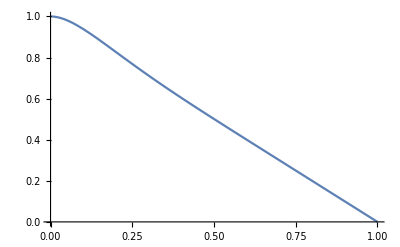

```mathematica
(* truncation loss is a problem here at low T *)
loss[T_] := 1-(T^2 Sum[(1-T)^i,{i,0,8}]) (* ignoring the first reflected mode *)
Plot[loss[T],{T,0,1},PlotRange->{0,1}]
```